```mathematica
CountryData["Countries"]
```

```mathematica
CountryData["China", "OilReserves"]
```

2.46488×10^10 bbl oil

```mathematica
CountryData["China","LandArea"]
```

9.32641×10^6 km^2

```mathematica
CountryData["Countries"][[1;;10]]
```

{Afghanistan,Albania,Algeria,American Samoa,Andorra,Angola,Anguilla,Antigua and Barbuda,Argentina,Armenia}

```mathematica
Sort[CountryData["Countries"], CountryData[#1, "OilReserves"]/CountryData[#1, "LandArea"] > CountryData[#2, "OilReserves"]/CountryData[#2, "LandArea"]&][[1;;10]]
```

{Iraq,Iran,Equatorial Guinea,Kazakhstan,Gabon,Albania,Algeria,Egypt,Indonesia,India}

```mathematica
1/2
```

1/2

# Question5

-Graphics-

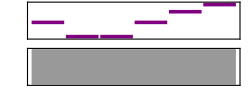

```mathematica
Sound[SoundNote[#,0.3]&/@(Characters[GenomeData["SCNN1A","FullSequence"]][[1877;;1882]]/."T"->"E")]
```

## Question7

```mathematica
text=ExampleData[{"Text","GettysburgAddress"}]
```